```mathematica
β[ω_,δ_,t_,ϵ_,m_]:=β[ω,δ,t,ϵ,m]=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[m],Join[Table[{i,i-1},{i,Range[2,m,1]}],Table[{i,i+1},{i,Range[1,m,1]}]]->-t]
```

```mathematica
T[t_,m_]:=T[t,m]=t*IdentityMatrix[m]
```

```mathematica
Clear[LEFT,LEFT1]
```

```mathematica
LEFT[ω_,δ_,t_,ϵ_,m_]:=LEFT[ω,δ,t,ϵ,m]=Module[{J=Inverse[β[ω,δ,1,0,m]],A:=Inverse[β[ω,δ,1,0,m]],T:=T[1,m]},Do[J=Inverse[IdentityMatrix[m]-A.T.J.T].A,16000];J=J]
```

```mathematica
g[ω_,δ_,t_,ϵ_,m_]:= Inverse[β[ω,δ,t,ϵ,m]]
```

```mathematica
SR[ω_,δ_,t_,ϵ_,m_]:=Inverse[IdentityMatrix[m]-g[ω,δ,t,ϵ,m].T[1,m].LEFT[ω,δ,t,ϵ,m].T[1,m]].g[ω,δ,t,ϵ,m]
```

```mathematica
SL[ω_,δ_,t_,ϵ_,m_]:=Inverse[IdentityMatrix[m]-g[ω,δ,t,ϵ,m].T[1,m].LEFT[ω,δ,t,ϵ,m].T[1,m]].g[ω,δ,t,ϵ,m]
```

```mathematica
IL[ω_,δ_,t_,ϵ_,m_]:=Inverse[IdentityMatrix[m]-SL[ω,δ,1,0,m].T[1,m].SR[ω,δ,1,0,m].T[1,m]].SL[ω,δ,1,0,m]
```

```mathematica
IR[ω_,δ_,t_,ϵ_,m_]:=Inverse[IdentityMatrix[m]-SR[ω,δ,1,0,m].T[1,m].SL[ω,δ,1,0,m].T[1,m]].SR[ω,δ,1,0,m]
```

```mathematica
gdd[ω_,δ_,t_,ϵ_,m_]:= IL[ω,δ,t,ϵ,m]-ConjugateTranspose[IL[ω,δ,t,ϵ,m]]
```

```mathematica
grr[ω_,δ_,t_,ϵ_,m_]:= IR[ω,δ,t,ϵ,m]-ConjugateTranspose[IR[ω,δ,t,ϵ,m]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ_,m_]:= SR[ω,δ,1,0,m].T[1,m].IL[ω,δ,t,ϵ,m]
```

```mathematica
GNON[ω_,δ_,t_,ϵ_,m_]:= Gnonlocal[ω,δ,t,ϵ,m]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ,m]]
```

```mathematica
tr[ω_,δ_,t_,ϵ_,m_]:=Abs[Tr[gdd[ω,δ,t,ϵ,m].T[1,m].grr[ω,δ,t,ϵ,m].T[1,m]-T[1,m].GNON[ω,δ,t,ϵ,m].T[1,m].GNON[ω,δ,t,ϵ,m]]]
```

```mathematica
tr[0,0.001,1,0,7]
```

6.99997

```mathematica
ρ[t_,m_]:=ρ[t,m] =t*IdentityMatrix[m]
```

```mathematica
κ[ω_,δ_,t_,ϵ_,ϵ1_,m_]:=κ[ω,δ,t,ϵ,ϵ1,m]=Module[{imp1=Inverse[Module[{i=β[ω,δ,t,ϵ,m],μ1=RandomInteger[{1,m}]},ReplacePart[i,{{1,1}}->ω+ⅈ*δ-ϵ1]]],imp2=Inverse[Module[{i=β[ω,δ,t,ϵ,m],μ1=RandomInteger[{1,m}]},ReplacePart[i,{{2,2}}->ω+ⅈ*δ-ϵ1]]],imp3=Inverse[Module[{i=β[ω,δ,t,ϵ,m],μ1=RandomInteger[{1,m}]},ReplacePart[i,{{3,3}}->ω+ⅈ*δ-ϵ1]]],imp4=Inverse[Module[{i=β[ω,δ,t,ϵ,m],μ1=RandomInteger[{1,m}]},ReplacePart[i,{{4,4}}->ω+ⅈ*δ-ϵ1]]],imp5=Inverse[Module[{i=β[ω,δ,t,ϵ,m],μ1=RandomInteger[{1,m}]},ReplacePart[i,{{5,5}}->ω+ⅈ*δ-ϵ1]]],imp7=Inverse[Module[{i=β[ω,δ,t,ϵ,m],μ1=RandomInteger[{1,m}]},ReplacePart[i,{{7,7}}->ω+ⅈ*δ-ϵ1]]],imp6=Inverse[Module[{i=β[ω,δ,t,ϵ,m],μ1=RandomInteger[{1,m}]},ReplacePart[i,{{6,6}}->ω+ⅈ*δ-ϵ1]]]},RandomChoice[{imp1,imp2,imp3,imp4,imp5,imp7,imp6},300]]
```

```mathematica
Table[Re[κ[0,0.001,0,0,1,7][[x]]],{x,100}]
```

{{{0.,0.,0.,0.,0.,0.,0.},{0.,-0.999999,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.}},{{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,-0.999999,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.}},{{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,-0.999999,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.}},{{0.,0.,0.,0.,0.,0.,0.},{0.,-0.999999,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.}},{{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,-0.999999,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.}},{{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,-0.999999}},{{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,-0.999999}},{{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,-0.999999,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.}},{{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,-0.999999,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.}},{{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,-0.999999,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.}},{{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,-0.999999,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.}},{{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,-0.999999,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.}},{{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,-0.999999,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.}},{{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,-0.999999,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.}},{{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,-0.999999,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.}},{{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,-0.999999,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.}},{{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,-0.999999,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.}},{{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,-0.999999,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.}},{{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,-0.999999,0.},{0.,0.,0.,0.,0.,0.,0.}},{{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,-0.999999,0.},{0.,0.,0.,0.,0.,0.,0.}},{{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,-0.999999,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.}},{{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,-0.999999,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.}},{{-0.999999,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.}},{{0.,0.,0.,0.,0.,0.,0.},{0.,-0.999999,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.}},{{0.,0.,0.,0.,0.,0.,0.},{0.,-0.999999,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.}},{{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,-0.999999,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.}},{{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,-0.999999,0.},{0.,0.,0.,0.,0.,0.,0.}},{{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,-0.999999,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.}},{{-0.999999,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.}},{{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,-0.999999,0.},{0.,0.,0.,0.,0.,0.,0.}},{{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,-0.999999,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.}},{{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,-0.999999}},{{-0.999999,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.}},{{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,-0.999999,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.}},{{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,-0.999999,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.}},{{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,-0.999999,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.}},{{-0.999999,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.}},{{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,-0.999999,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.}},{{0.,0.,0.,0.,0.,0.,0.},{0.,-0.999999,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.}},{{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,-0.999999,0.},{0.,0.,0.,0.,0.,0.,0.}},{{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,-0.999999,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.}},{{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,-0.999999,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.}},{{-0.999999,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.}},{{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,-0.999999}},{{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,-0.999999,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.}},{{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,-0.999999,0.},{0.,0.,0.,0.,0.,0.,0.}},{{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,-0.999999,0.},{0.,0.,0.,0.,0.,0.,0.}},{{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,-0.999999,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.}},{{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,-0.999999,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.}},{{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,-0.999999,0.},{0.,0.,0.,0.,0.,0.,0.}},{{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,-0.999999,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.}},{{0.,0.,0.,0.,0.,0.,0.},{0.,-0.999999,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.}},{{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,-0.999999,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.}},{{-0.999999,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.}},{{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,-0.999999,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.}},{{-0.999999,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.}},{{-0.999999,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.}},{{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,-0.999999,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.}},{{-0.999999,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.}},{{0.,0.,0.,0.,0.,0.,0.},{0.,-0.999999,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.}},{{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,-0.999999,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.}},{{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,-0.999999}},{{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,-0.999999,0.},{0.,0.,0.,0.,0.,0.,0.}},{{-0.999999,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.}},{{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,-0.999999,0.},{0.,0.,0.,0.,0.,0.,0.}},{{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,-0.999999}},{{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,-0.999999,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.}},{{-0.999999,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.}},{{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,-0.999999}},{{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,-0.999999,0.},{0.,0.,0.,0.,0.,0.,0.}},{{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,-0.999999,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.}},{{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,-0.999999,0.},{0.,0.,0.,0.,0.,0.,0.}},{{0.,0.,0.,0.,0.,0.,0.},{0.,-0.999999,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.}},{{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,-0.999999,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.}},{{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,-0.999999,0.},{0.,0.,0.,0.,0.,0.,0.}},{{0.,0.,0.,0.,0.,0.,0.},{0.,-0.999999,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.}},{{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,-0.999999,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.}},{{0.,0.,0.,0.,0.,0.,0.},{0.,-0.999999,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.}},{{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,-0.999999,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.}},{{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,-0.999999}},{{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,-0.999999}},{{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,-0.999999,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.}},{{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,-0.999999}},{{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,-0.999999,0.},{0.,0.,0.,0.,0.,0.,0.}},{{0.,0.,0.,0.,0.,0.,0.},{0.,-0.999999,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.}},{{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,-0.999999,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.}},{{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,-0.999999,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.}},{{0.,0.,0.,0.,0.,0.,0.},{0.,-0.999999,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.}},{{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,-0.999999,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.}},{{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,-0.999999,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.}},{{-0.999999,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.}},{{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,-0.999999,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.}},{{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,-0.999999,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.}},{{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,-0.999999,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.}},{{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,-0.999999,0.},{0.,0.,0.,0.,0.,0.,0.}},{{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,-0.999999,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.}},{{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,-0.999999,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.}},{{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,-0.999999,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.}},{{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,-0.999999,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.}},{{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,-0.999999,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.}}}

```mathematica
tr1[ω_,δ_,t_,ϵ_,ϵ1_,m_]:=Module[{gg=g[ω,δ,t,ϵ,m],T=ρ[1,m]},η=Module[{},
sl1=Module[{J=SR[ω,δ,t,ϵ,m]},Do[J=
Inverse[IdentityMatrix[m]-κ[ω,0.001,1,0,ϵ1,m][[i]].ConjugateTranspose[T].J.T].κ[ω,0.001,1,0,ϵ1,m][[i]],{i,7}]; J=J]; 
Il1:=Inverse[IdentityMatrix[m]-sl1.ρ[1,m].SR[ω,δ,t,ϵ,m].ρ[1,m]].sl1;Ir1:=Inverse[IdentityMatrix[m]-SR[ω,δ,t,ϵ,m].ρ[1,m].sl1.ρ[1,m]].SR[ω,δ,t,ϵ,m];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,δ,t,ϵ,m].ρ[1,m].Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];Abs[Tr[gdd1.ρ[1,m].grr1.ρ[1,m]-ρ[1,m].GNON1.ρ[1,m].GNON1]]];
η]
```

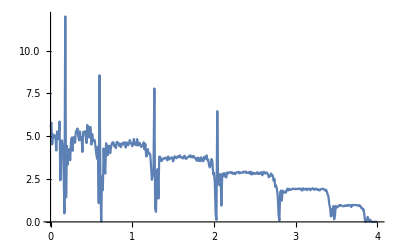

```mathematica
ListLinePlot[Table[{ω,tr1[ω,0.001,1,0,0.5,7]},{ω,Range[0,4,0.01]}]]
```

```mathematica
Timing[Mean[Table[tr1[0,0.001,1,0,1,7],2500]]]
```

{11.5997,2.90668}

```mathematica
Table[{ω,Mean[Table[tr1[ω,0.001,1,0,1,8],2500]]},{ω,Range[0,4,0.01]}]
```

{{0.,3.68142},{0.01,3.73356},{0.02,3.70802},{0.03,3.86823},{0.04,3.85681},{0.05,3.98182},{0.06,4.08582},{0.07,4.41322},{0.08,4.7849},{0.09,5.28105},{0.1,6.14857},{0.11,7.43632},{0.12,11.5546},{0.13,11.4745},{0.14,9.96708},{0.15,8.95001},{0.16,7.6912},{0.17,6.92394},{0.18,6.09495},{0.19,5.39231},{0.2,4.74948},{0.21,4.05966},{0.22,3.69789},{0.23,3.31721},{0.24,2.94232},{0.25,2.61657},{0.26,2.41787},{0.27,2.16808},{0.28,1.99467},{0.29,1.92436},{0.3,1.82864},{0.31,1.77487},{0.32,1.75918},{0.33,1.70212},{0.34,1.69684},{0.35,1.70137},{0.36,1.77202},{0.37,1.80612},{0.38,1.91815},{0.39,1.99308},{0.4,2.15724},{0.41,2.31913},{0.42,2.52518},{0.43,2.86132},{0.44,3.25196},{0.45,3.95913},{0.46,5.2559},{0.47,8.51657},{0.48,7.77296},{0.49,7.00676},{0.5,6.42311},{0.51,5.6163},{0.52,4.96178},{0.53,4.55597},{0.54,3.92488},{0.55,3.42679},{0.56,3.02248},{0.57,2.64293},{0.58,2.24937},{0.59,1.92846},{0.6,1.74959},{0.61,1.43132},{0.62,1.1862},{0.63,1.04986},{0.64,0.919474},{0.65,0.80653},{0.66,0.728398},{0.67,0.648636},{0.68,0.594539},{0.69,0.567854},{0.7,0.530525},{0.71,0.517898},{0.72,0.518214},{0.73,0.479707},{0.74,0.480386},{0.75,0.464371},{0.76,0.478356},{0.77,0.463992},{0.78,0.457782},{0.79,0.467459},{0.8,0.47609},{0.81,0.483887},{0.82,0.48915},{0.83,0.479726},{0.84,0.511232},{0.85,0.516851},{0.86,0.542961},{0.87,0.558618},{0.88,0.575648},{0.89,0.633831},{0.9,0.667788},{0.91,0.751958},{0.92,0.793319},{0.93,0.87012},{0.94,1.02429},{0.95,1.19163},{0.96,1.41277},{0.97,1.68236},{0.98,2.16788},{0.99,3.03005},{1.,5.58466},{1.01,5.69123},{1.02,5.193},{1.03,4.76889},{1.04,4.21918},{1.05,3.85116},{1.06,3.41845},{1.07,2.95127},{1.08,2.73748},{1.09,2.33442},{1.1,2.0702},{1.11,1.77051},{1.12,1.52611},{1.13,1.24088},{1.14,1.05774},{1.15,0.918862},{1.16,0.780085},{1.17,0.643822},{1.18,0.585832},{1.19,0.52817},{1.2,0.51132},{1.21,0.467578},{1.22,0.465604},{1.23,0.502762},{1.24,0.480341},{1.25,0.501212},{1.26,0.512475},{1.27,0.535133},{1.28,0.555286},{1.29,0.558856},{1.3,0.577921},{1.31,0.582964},{1.32,0.598359},{1.33,0.619936},{1.34,0.619477},{1.35,0.622991},{1.36,0.62835},{1.37,0.611375},{1.38,0.62927},{1.39,0.617875},{1.4,0.620484},{1.41,0.612883},{1.42,0.595325},{1.43,0.593628},{1.44,0.58753},{1.45,0.579108},{1.46,0.55377},{1.47,0.559708},{1.48,0.530505},{1.49,0.522441},{1.5,0.509408},{1.51,0.510716},{1.52,0.483676},{1.53,0.47278},{1.54,0.465157},{1.55,0.459739},{1.56,0.467567},{1.57,0.483721},{1.58,0.491453},{1.59,0.547022},{1.6,0.609881},{1.61,0.697497},{1.62,0.892476},{1.63,1.18608},{1.64,1.66985},{1.65,2.88986},{1.66,4.00385},{1.67,3.69931},{1.68,3.40102},{1.69,3.1688},{1.7,3.0212},{1.71,2.54609},{1.72,2.35393},{1.73,2.1635},{1.74,1.9935},{1.75,1.66151},{1.76,1.49989},{1.77,1.26295},{1.78,1.14162},{1.79,1.01115},{1.8,0.838805},{1.81,0.718701},{1.82,0.636759},{1.83,0.565159},{1.84,0.514966},{1.85,0.50806},{1.86,0.498172},{1.87,0.515374},{1.88,0.546163},{1.89,0.566641},{1.9,0.590032},{1.91,0.630343},{1.92,0.653841},{1.93,0.67097},{1.94,0.681176},{1.95,0.694352},{1.96,0.705289},{1.97,0.729133},{1.98,0.739108},{1.99,0.737787},{2.,0.760377},{2.01,0.756963},{2.02,0.772241},{2.03,0.778648},{2.04,0.762568},{2.05,0.764399},{2.06,0.761774},{2.07,0.779776},{2.08,0.762469},{2.09,0.761386},{2.1,0.762548},{2.11,0.737992},{2.12,0.725354},{2.13,0.726241},{2.14,0.709142},{2.15,0.702617},{2.16,0.684182},{2.17,0.671654},{2.18,0.656148},{2.19,0.628387},{2.2,0.61109},{2.21,0.591156},{2.22,0.566033},{2.23,0.553266},{2.24,0.530958},{2.25,0.514391},{2.26,0.488558},{2.27,0.466591},{2.28,0.45968},{2.29,0.466471},{2.3,0.490735},{2.31,0.547396},{2.32,0.648412},{2.33,0.868326},{2.34,1.40549},{2.35,3.03048},{2.36,2.86873},{2.37,2.86386},{2.38,2.5754},{2.39,2.47919},{2.4,2.18514},{2.41,2.13168},{2.42,1.90616},{2.43,1.72579},{2.44,1.58015},{2.45,1.48172},{2.46,1.37296},{2.47,1.17393},{2.48,1.00559},{2.49,0.886643},{2.5,0.792263},{2.51,0.692401},{2.52,0.595816},{2.53,0.533822},{2.54,0.510064},{2.55,0.504697},{2.56,0.502691},{2.57,0.518982},{2.58,0.521508},{2.59,0.556282},{2.6,0.589121},{2.61,0.610211},{2.62,0.636195},{2.63,0.649657},{2.64,0.656675},{2.65,0.684945},{2.66,0.702989},{2.67,0.722782},{2.68,0.717482},{2.69,0.72646},{2.7,0.724767},{2.71,0.716355},{2.72,0.728274},{2.73,0.728899},{2.74,0.739883},{2.75,0.724949},{2.76,0.719303},{2.77,0.71718},{2.78,0.720182},{2.79,0.697734},{2.8,0.704877},{2.81,0.694287},{2.82,0.677259},{2.83,0.663716},{2.84,0.651401},{2.85,0.639875},{2.86,0.612317},{2.87,0.615247},{2.88,0.580973},{2.89,0.576682},{2.9,0.550295},{2.91,0.51529},{2.92,0.505144},{2.93,0.476727},{2.94,0.454686},{2.95,0.445164},{2.96,0.436998},{2.97,0.461976},{2.98,0.537823},{2.99,0.764178},{3.,1.80455},{3.01,2.12238},{3.02,1.98505},{3.03,2.07525},{3.04,1.87478},{3.05,1.80258},{3.06,1.63587},{3.07,1.56616},{3.08,1.51156},{3.09,1.39544},{3.1,1.27906},{3.11,1.12881},{3.12,1.06146},{3.13,0.920461},{3.14,0.814421},{3.15,0.681236},{3.16,0.627312},{3.17,0.537668},{3.18,0.447338},{3.19,0.419553},{3.2,0.392166},{3.21,0.39153},{3.22,0.396096},{3.23,0.429688},{3.24,0.445874},{3.25,0.466191},{3.26,0.47535},{3.27,0.492829},{3.28,0.516042},{3.29,0.516987},{3.3,0.529998},{3.31,0.522458},{3.32,0.529389},{3.33,0.528503},{3.34,0.550737},{3.35,0.533856},{3.36,0.535077},{3.37,0.528565},{3.38,0.528788},{3.39,0.511402},{3.4,0.517177},{3.41,0.487157},{3.42,0.477612},{3.43,0.477821},{3.44,0.469207},{3.45,0.449897},{3.46,0.428844},{3.47,0.423425},{3.48,0.408702},{3.49,0.389524},{3.5,0.378972},{3.51,0.399963},{3.52,0.451799},{3.53,0.798599},{3.54,1.61851},{3.55,1.50286},{3.56,1.43838},{3.57,1.45278},{3.58,1.37335},{3.59,1.26802},{3.6,1.21294},{3.61,1.15138},{3.62,1.01068},{3.63,1.11756},{3.64,0.919006},{3.65,0.977405},{3.66,0.83214},{3.67,0.695473},{3.68,0.672201},{3.69,0.5764},{3.7,0.495895},{3.71,0.460404},{3.72,0.382973},{3.73,0.3448},{3.74,0.289599},{3.75,0.305133},{3.76,0.288358},{3.77,0.302222},{3.78,0.30913},{3.79,0.306509},{3.8,0.308691},{3.81,0.312257},{3.82,0.30832},{3.83,0.306214},{3.84,0.301356},{3.85,0.282375},{3.86,0.271852},{3.87,0.287562},{3.88,0.914535},{3.89,1.26775},{3.9,1.30056},{3.91,1.41705},{3.92,0.97419},{3.93,1.05961},{3.94,0.832756},{3.95,0.731965},{3.96,0.832073},{3.97,0.618282},{3.98,0.787078},{3.99,0.561373},{4.,0.483724}}

```mathematica
Table[{ω,Mean[Table[tr1[ω,0.001,1,0,1,9],2500]]},{ω,Range[0,4,0.01]}]
```

{{0.,4.55993},{0.01,4.513},{0.02,4.58998},{0.03,4.80065},{0.04,4.955},{0.05,5.20891},{0.06,5.65362},{0.07,6.26158},{0.08,7.13341},{0.09,9.13454},{0.1,13.8039},{0.11,11.9683},{0.12,10.34},{0.13,8.95864},{0.14,7.68836},{0.15,6.78803},{0.16,5.86963},{0.17,5.11409},{0.18,4.54177},{0.19,3.95245},{0.2,3.49722},{0.21,3.26578},{0.22,2.9461},{0.23,2.71924},{0.24,2.54912},{0.25,2.41846},{0.26,2.32086},{0.27,2.28564},{0.28,2.28722},{0.29,2.26992},{0.3,2.41082},{0.31,2.4981},{0.32,2.6022},{0.33,2.81951},{0.34,3.14231},{0.35,3.5195},{0.36,4.10722},{0.37,5.20897},{0.38,7.93335},{0.39,9.10933},{0.4,7.82451},{0.41,6.94657},{0.42,6.05013},{0.43,5.31315},{0.44,4.78878},{0.45,4.13092},{0.46,3.56396},{0.47,3.06523},{0.48,2.57232},{0.49,2.18405},{0.5,1.85308},{0.51,1.60861},{0.52,1.34113},{0.53,1.17177},{0.54,0.986861},{0.55,0.901301},{0.56,0.825224},{0.57,0.722645},{0.58,0.673186},{0.59,0.623133},{0.6,0.617031},{0.61,0.578624},{0.62,0.598158},{0.63,0.575835},{0.64,0.593895},{0.65,0.569631},{0.66,0.587625},{0.67,0.582831},{0.68,0.60212},{0.69,0.64051},{0.7,0.646835},{0.71,0.687554},{0.72,0.720321},{0.73,0.763989},{0.74,0.872226},{0.75,0.949358},{0.76,1.08652},{0.77,1.25549},{0.78,1.45592},{0.79,1.7458},{0.8,2.16216},{0.81,2.91333},{0.82,4.46858},{0.83,6.56717},{0.84,5.89951},{0.85,5.25947},{0.86,4.62522},{0.87,4.18586},{0.88,3.48733},{0.89,3.1519},{0.9,2.7688},{0.91,2.36683},{0.92,2.00068},{0.93,1.66002},{0.94,1.37069},{0.95,1.15163},{0.96,0.934034},{0.97,0.75917},{0.98,0.677092},{0.99,0.578435},{1.,0.544795},{1.01,0.52266},{1.02,0.506296},{1.03,0.510363},{1.04,0.537297},{1.05,0.545685},{1.06,0.560152},{1.07,0.567261},{1.08,0.593507},{1.09,0.60235},{1.1,0.616079},{1.11,0.627926},{1.12,0.63158},{1.13,0.621984},{1.14,0.628108},{1.15,0.640542},{1.16,0.644029},{1.17,0.630678},{1.18,0.632435},{1.19,0.620598},{1.2,0.592077},{1.21,0.588338},{1.22,0.575172},{1.23,0.565341},{1.24,0.557811},{1.25,0.537965},{1.26,0.520014},{1.27,0.491665},{1.28,0.485914},{1.29,0.486713},{1.3,0.493135},{1.31,0.52788},{1.32,0.574921},{1.33,0.665754},{1.34,0.808414},{1.35,0.981475},{1.36,1.37164},{1.37,1.9366},{1.38,3.65814},{1.39,4.62925},{1.4,4.26201},{1.41,3.78027},{1.42,3.29309},{1.43,3.03128},{1.44,2.69703},{1.45,2.39005},{1.46,2.11287},{1.47,1.78522},{1.48,1.53968},{1.49,1.25364},{1.5,1.08253},{1.51,0.875488},{1.52,0.740918},{1.53,0.650497},{1.54,0.611399},{1.55,0.5761},{1.56,0.570032},{1.57,0.593161},{1.58,0.630467},{1.59,0.674798},{1.6,0.693201},{1.61,0.732688},{1.62,0.754819},{1.63,0.796079},{1.64,0.830296},{1.65,0.827884},{1.66,0.859317},{1.67,0.870426},{1.68,0.891764},{1.69,0.904868},{1.7,0.924213},{1.71,0.922822},{1.72,0.925784},{1.73,0.91257},{1.74,0.913505},{1.75,0.914797},{1.76,0.911391},{1.77,0.884059},{1.78,0.888847},{1.79,0.887456},{1.8,0.882448},{1.81,0.856124},{1.82,0.842935},{1.83,0.804835},{1.84,0.786796},{1.85,0.776373},{1.86,0.740944},{1.87,0.715058},{1.88,0.673565},{1.89,0.656301},{1.9,0.624979},{1.91,0.573144},{1.92,0.570313},{1.93,0.523194},{1.94,0.514895},{1.95,0.508809},{1.96,0.54578},{1.97,0.644651},{1.98,0.86982},{1.99,1.3097},{2.,3.2025},{2.01,3.42385},{2.02,3.09258},{2.03,2.69716},{2.04,2.54249},{2.05,2.40885},{2.06,2.17763},{2.07,1.89991},{2.08,1.77711},{2.09,1.61077},{2.1,1.40888},{2.11,1.21233},{2.12,1.11148},{2.13,0.957655},{2.14,0.8405},{2.15,0.720481},{2.16,0.701753},{2.17,0.659453},{2.18,0.630909},{2.19,0.641404},{2.2,0.642813},{2.21,0.666451},{2.22,0.70481},{2.23,0.738043},{2.24,0.780942},{2.25,0.813915},{2.26,0.842531},{2.27,0.854056},{2.28,0.870655},{2.29,0.880361},{2.3,0.895594},{2.31,0.90508},{2.32,0.917385},{2.33,0.933754},{2.34,0.912616},{2.35,0.945582},{2.36,0.929517},{2.37,0.92614},{2.38,0.929478},{2.39,0.923377},{2.4,0.91022},{2.41,0.884301},{2.42,0.892228},{2.43,0.8747},{2.44,0.861131},{2.45,0.847256},{2.46,0.821468},{2.47,0.816457},{2.48,0.793366},{2.49,0.740559},{2.5,0.747272},{2.51,0.705043},{2.52,0.681782},{2.53,0.622776},{2.54,0.593},{2.55,0.545488},{2.56,0.530991},{2.57,0.502484},{2.58,0.488837},{2.59,0.516938},{2.6,0.661536},{2.61,1.03872},{2.62,2.61141},{2.63,2.68502},{2.64,2.3484},{2.65,2.21766},{2.66,2.08543},{2.67,1.95322},{2.68,1.80225},{2.69,1.6779},{2.7,1.49272},{2.71,1.3207},{2.72,1.19665},{2.73,1.04183},{2.74,0.899445},{2.75,0.78627},{2.76,0.661712},{2.77,0.598874},{2.78,0.539216},{2.79,0.516969},{2.8,0.530209},{2.81,0.552111},{2.82,0.597047},{2.83,0.607946},{2.84,0.651135},{2.85,0.678327},{2.86,0.706178},{2.87,0.741891},{2.88,0.735947},{2.89,0.762419},{2.9,0.767809},{2.91,0.779168},{2.92,0.794765},{2.93,0.795823},{2.94,0.812574},{2.95,0.808762},{2.96,0.788143},{2.97,0.787167},{2.98,0.795997},{2.99,0.777584},{3.,0.775522},{3.01,0.761616},{3.02,0.747149},{3.03,0.736492},{3.04,0.710042},{3.05,0.701505},{3.06,0.677164},{3.07,0.657088},{3.08,0.645385},{3.09,0.596285},{3.1,0.57925},{3.11,0.541866},{3.12,0.512926},{3.13,0.480389},{3.14,0.451861},{3.15,0.461634},{3.16,0.54573},{3.17,0.840862},{3.18,1.93666},{3.19,1.89239},{3.2,1.85881},{3.21,1.57061},{3.22,1.55825},{3.23,1.54291},{3.24,1.49634},{3.25,1.2758},{3.26,1.1976},{3.27,1.07528},{3.28,1.03023},{3.29,0.836089},{3.3,0.785127},{3.31,0.67017},{3.32,0.574798},{3.33,0.480208},{3.34,0.42866},{3.35,0.426305},{3.36,0.418361},{3.37,0.417779},{3.38,0.428054},{3.39,0.459601},{3.4,0.488712},{3.41,0.498382},{3.42,0.524116},{3.43,0.526853},{3.44,0.542016},{3.45,0.535681},{3.46,0.534287},{3.47,0.550176},{3.48,0.545954},{3.49,0.53974},{3.5,0.523087},{3.51,0.523951},{3.52,0.503889},{3.53,0.488685},{3.54,0.481936},{3.55,0.46636},{3.56,0.451344},{3.57,0.430009},{3.58,0.403003},{3.59,0.399686},{3.6,0.398419},{3.61,0.47787},{3.62,1.39142},{3.63,1.46839},{3.64,1.3563},{3.65,1.37944},{3.66,1.34437},{3.67,1.1117},{3.68,1.08489},{3.69,1.11074},{3.7,0.957234},{3.71,0.904486},{3.72,0.931981},{3.73,0.842787},{3.74,0.750833},{3.75,0.72765},{3.76,0.57556},{3.77,0.506342},{3.78,0.471209},{3.79,0.387704},{3.8,0.338367},{3.81,0.321068},{3.82,0.315405},{3.83,0.289485},{3.84,0.303112},{3.85,0.30143},{3.86,0.304152},{3.87,0.299092},{3.88,0.295531},{3.89,0.292553},{3.9,0.495121},{3.91,1.31995},{3.92,1.44613},{3.93,1.32239},{3.94,1.16023},{3.95,1.19532},{3.96,0.876723},{3.97,0.790102},{3.98,1.02187},{3.99,0.702249},{4.,0.490396}}

```mathematica
Table[{ω,Mean[Table[tr1[ω,0.001,1,0,1,10],2500]]},{ω,Range[0,4,0.01]}]
```

{{0.,5.44271},{0.01,5.45405},{0.02,5.65883},{0.03,5.88073},{0.04,6.20731},{0.05,6.67239},{0.06,7.5671},{0.07,9.19309},{0.08,13.6423},{0.09,13.5098},{0.1,11.6103},{0.11,9.94577},{0.12,8.49634},{0.13,7.33281},{0.14,6.14544},{0.15,5.48208},{0.16,4.72062},{0.17,4.25798},{0.18,3.82847},{0.19,3.45908},{0.2,3.23861},{0.21,3.09423},{0.22,2.95543},{0.23,2.95508},{0.24,2.93355},{0.25,2.98418},{0.26,3.19557},{0.27,3.43281},{0.28,3.72122},{0.29,4.27624},{0.3,5.09341},{0.31,6.74033},{0.32,10.6158},{0.33,9.21154},{0.34,8.08042},{0.35,6.69442},{0.36,5.81072},{0.37,5.24466},{0.38,4.34875},{0.39,3.75878},{0.4,3.34866},{0.41,2.64564},{0.42,2.25003},{0.43,1.92237},{0.44,1.59388},{0.45,1.37569},{0.46,1.22656},{0.47,1.04469},{0.48,0.954929},{0.49,0.883648},{0.5,0.823301},{0.51,0.779749},{0.52,0.72728},{0.53,0.745656},{0.54,0.745702},{0.55,0.744026},{0.56,0.755823},{0.57,0.785287},{0.58,0.820905},{0.59,0.8926},{0.6,0.949518},{0.61,1.01638},{0.62,1.1255},{0.63,1.28266},{0.64,1.47329},{0.65,1.74197},{0.66,2.15786},{0.67,2.71817},{0.68,3.65428},{0.69,7.03178},{0.7,6.68625},{0.71,6.02937},{0.72,5.21132},{0.73,4.40195},{0.74,3.94124},{0.75,3.40421},{0.76,2.78961},{0.77,2.31429},{0.78,1.9811},{0.79,1.52318},{0.8,1.26064},{0.81,1.02117},{0.82,0.848144},{0.83,0.718701},{0.84,0.627466},{0.85,0.585759},{0.86,0.548109},{0.87,0.557666},{0.88,0.560549},{0.89,0.558644},{0.9,0.561621},{0.91,0.585938},{0.92,0.598162},{0.93,0.603812},{0.94,0.614119},{0.95,0.622219},{0.96,0.63081},{0.97,0.635967},{0.98,0.630232},{0.99,0.636861},{1.,0.612662},{1.01,0.611239},{1.02,0.57816},{1.03,0.568544},{1.04,0.560946},{1.05,0.535711},{1.06,0.523812},{1.07,0.512601},{1.08,0.516044},{1.09,0.523251},{1.1,0.562124},{1.11,0.612783},{1.12,0.724115},{1.13,0.897236},{1.14,1.18272},{1.15,1.6228},{1.16,2.4792},{1.17,5.44088},{1.18,5.02284},{1.19,4.48832},{1.2,4.01257},{1.21,3.52574},{1.22,3.06052},{1.23,2.48669},{1.24,2.16254},{1.25,1.73644},{1.26,1.43962},{1.27,1.20138},{1.28,1.03295},{1.29,0.826374},{1.3,0.719239},{1.31,0.650978},{1.32,0.652489},{1.33,0.66551},{1.34,0.691944},{1.35,0.741515},{1.36,0.779227},{1.37,0.821396},{1.38,0.850798},{1.39,0.88453},{1.4,0.923239},{1.41,0.963909},{1.42,0.975074},{1.43,0.991165},{1.44,1.01558},{1.45,1.0356},{1.46,1.0207},{1.47,1.01316},{1.48,1.02849},{1.49,1.03115},{1.5,1.02057},{1.51,1.00891},{1.52,0.995221},{1.53,0.99546},{1.54,0.966133},{1.55,0.939221},{1.56,0.933166},{1.57,0.890101},{1.58,0.859338},{1.59,0.828884},{1.6,0.794346},{1.61,0.735507},{1.62,0.706143},{1.63,0.631051},{1.64,0.605157},{1.65,0.552163},{1.66,0.536799},{1.67,0.544101},{1.68,0.619161},{1.69,0.785601},{1.7,1.13706},{1.71,2.03301},{1.72,4.15363},{1.73,3.57134},{1.74,3.18752},{1.75,2.87737},{1.76,2.39437},{1.77,2.23781},{1.78,1.96657},{1.79,1.61301},{1.8,1.43411},{1.81,1.20311},{1.82,1.01725},{1.83,0.834802},{1.84,0.746328},{1.85,0.667241},{1.86,0.666509},{1.87,0.673427},{1.88,0.730284},{1.89,0.779627},{1.9,0.834536},{1.91,0.880647},{1.92,0.936539},{1.93,1.00069},{1.94,1.02715},{1.95,1.04443},{1.96,1.07129},{1.97,1.0938},{1.98,1.11835},{1.99,1.1241},{2.,1.11996},{2.01,1.14436},{2.02,1.13798},{2.03,1.14503},{2.04,1.13242},{2.05,1.12971},{2.06,1.12619},{2.07,1.1286},{2.08,1.11877},{2.09,1.09005},{2.1,1.07783},{2.11,1.05681},{2.12,1.04402},{2.13,1.02603},{2.14,0.994073},{2.15,0.961602},{2.16,0.932413},{2.17,0.882486},{2.18,0.848451},{2.19,0.782977},{2.2,0.742377},{2.21,0.692871},{2.22,0.625472},{2.23,0.577473},{2.24,0.548234},{2.25,0.521929},{2.26,0.597172},{2.27,0.827523},{2.28,1.59774},{2.29,2.98183},{2.3,2.87315},{2.31,2.54712},{2.32,2.41258},{2.33,2.1502},{2.34,1.92899},{2.35,1.69618},{2.36,1.55495},{2.37,1.3211},{2.38,1.20368},{2.39,1.02276},{2.4,0.888993},{2.41,0.761207},{2.42,0.697846},{2.43,0.649795},{2.44,0.657214},{2.45,0.681256},{2.46,0.716743},{2.47,0.778212},{2.48,0.809009},{2.49,0.874428},{2.5,0.903221},{2.51,0.943956},{2.52,0.972707},{2.53,0.986461},{2.54,1.02589},{2.55,1.03799},{2.56,1.04914},{2.57,1.06562},{2.58,1.06145},{2.59,1.06287},{2.6,1.06547},{2.61,1.06159},{2.62,1.03803},{2.63,1.02558},{2.64,1.04262},{2.65,1.02707},{2.66,1.00294},{2.67,0.986051},{2.68,0.966273},{2.69,0.963476},{2.7,0.917933},{2.71,0.909335},{2.72,0.862631},{2.73,0.84546},{2.74,0.805589},{2.75,0.751629},{2.76,0.69587},{2.77,0.654842},{2.78,0.586047},{2.79,0.557163},{2.8,0.516876},{2.81,0.534258},{2.82,0.745095},{2.83,1.75},{2.84,2.18239},{2.85,2.18788},{2.86,1.98092},{2.87,1.81158},{2.88,1.6847},{2.89,1.46254},{2.9,1.46238},{2.91,1.28671},{2.92,1.082},{2.93,0.984149},{2.94,0.842233},{2.95,0.723015},{2.96,0.658842},{2.97,0.615094},{2.98,0.562763},{2.99,0.552607},{3.,0.55641},{3.01,0.627857},{3.02,0.651431},{3.03,0.710172},{3.04,0.750094},{3.05,0.77198},{3.06,0.792597},{3.07,0.81076},{3.08,0.818677},{3.09,0.833843},{3.1,0.844493},{3.11,0.840079},{3.12,0.834917},{3.13,0.8232},{3.14,0.822654},{3.15,0.826917},{3.16,0.811245},{3.17,0.811573},{3.18,0.781542},{3.19,0.773009},{3.2,0.746835},{3.21,0.726454},{3.22,0.696323},{3.23,0.664144},{3.24,0.632929},{3.25,0.588047},{3.26,0.561081},{3.27,0.514962},{3.28,0.480406},{3.29,0.46892},{3.3,0.578237},{3.31,1.49132},{3.32,1.86682},{3.33,1.67091},{3.34,1.60453},{3.35,1.44636},{3.36,1.37842},{3.37,1.17136},{3.38,1.12792},{3.39,1.07904},{3.4,0.931073},{3.41,0.884647},{3.42,0.73594},{3.43,0.67775},{3.44,0.570815},{3.45,0.492853},{3.46,0.466792},{3.47,0.419785},{3.48,0.429191},{3.49,0.442137},{3.5,0.467226},{3.51,0.483381},{3.52,0.498243},{3.53,0.523949},{3.54,0.540092},{3.55,0.546913},{3.56,0.543348},{3.57,0.522673},{3.58,0.534658},{3.59,0.524856},{3.6,0.508802},{3.61,0.504062},{3.62,0.465966},{3.63,0.46917},{3.64,0.425267},{3.65,0.406063},{3.66,0.401299},{3.67,0.417752},{3.68,0.664757},{3.69,1.34394},{3.7,1.26778},{3.71,1.3246},{3.72,1.20725},{3.73,1.10774},{3.74,1.06181},{3.75,1.03452},{3.76,0.977407},{3.77,0.855363},{3.78,0.826048},{3.79,0.769725},{3.8,0.674379},{3.81,0.601526},{3.82,0.516073},{3.83,0.447178},{3.84,0.377038},{3.85,0.361904},{3.86,0.33664},{3.87,0.320083},{3.88,0.313151},{3.89,0.303633},{3.9,0.30921},{3.91,0.35141},{3.92,1.11989},{3.93,1.50655},{3.94,1.46724},{3.95,1.22688},{3.96,1.11673},{3.97,0.922036},{3.98,0.87352},{3.99,0.746989},{4.,0.73186}}

```mathematica
Table[{ω,Mean[Table[tr1[ω,0.001,1,0,1,11],2500]]},{ω,Range[0,4,0.01]}]
```

{{0.,6.3967},{0.01,6.62067},{0.02,6.76677},{0.03,7.16975},{0.04,7.65074},{0.05,8.70199},{0.06,10.7849},{0.07,16.8058},{0.08,13.8014},{0.09,11.6559},{0.1,9.78136},{0.11,8.32599},{0.12,7.21854},{0.13,6.19187},{0.14,5.31378},{0.15,4.76152},{0.16,4.2494},{0.17,3.97187},{0.18,3.77195},{0.19,3.61249},{0.2,3.69929},{0.21,3.74969},{0.22,3.89451},{0.23,4.19599},{0.24,4.65886},{0.25,5.59921},{0.26,7.25098},{0.27,11.4315},{0.28,10.0228},{0.29,8.64327},{0.3,7.18022},{0.31,6.17116},{0.32,5.14348},{0.33,4.3519},{0.34,3.68492},{0.35,3.00538},{0.36,2.57122},{0.37,2.16394},{0.38,1.79342},{0.39,1.52737},{0.4,1.41329},{0.41,1.20215},{0.42,1.1199},{0.43,1.03667},{0.44,0.989874},{0.45,0.983718},{0.46,0.975443},{0.47,0.979573},{0.48,0.994783},{0.49,1.05582},{0.5,1.13056},{0.51,1.20436},{0.52,1.35233},{0.53,1.55186},{0.54,1.78077},{0.55,2.11224},{0.56,2.66572},{0.57,3.42945},{0.58,5.08038},{0.59,7.94164},{0.6,6.86565},{0.61,5.91401},{0.62,5.06359},{0.63,4.28484},{0.64,3.69592},{0.65,2.94533},{0.66,2.39657},{0.67,1.90278},{0.68,1.53839},{0.69,1.22357},{0.7,1.00691},{0.71,0.782451},{0.72,0.68088},{0.73,0.611267},{0.74,0.579305},{0.75,0.561885},{0.76,0.584341},{0.77,0.571424},{0.78,0.588027},{0.79,0.584388},{0.8,0.608101},{0.81,0.615198},{0.82,0.610515},{0.83,0.609946},{0.84,0.594592},{0.85,0.604722},{0.86,0.59783},{0.87,0.576102},{0.88,0.580456},{0.89,0.56067},{0.9,0.547188},{0.91,0.546054},{0.92,0.568129},{0.93,0.590241},{0.94,0.64193},{0.95,0.732418},{0.96,0.92139},{0.97,1.20586},{0.98,1.70553},{0.99,2.61203},{1.,5.58108},{1.01,5.43762},{1.02,4.92957},{1.03,4.22667},{1.04,3.62476},{1.05,3.05894},{1.06,2.5046},{1.07,2.05426},{1.08,1.687},{1.09,1.25961},{1.1,0.978867},{1.11,0.837329},{1.12,0.730726},{1.13,0.693341},{1.14,0.694106},{1.15,0.739259},{1.16,0.780422},{1.17,0.841713},{1.18,0.900306},{1.19,0.95549},{1.2,0.993875},{1.21,1.02828},{1.22,1.06492},{1.23,1.08056},{1.24,1.08937},{1.25,1.108},{1.26,1.12337},{1.27,1.1134},{1.28,1.10314},{1.29,1.11833},{1.3,1.09778},{1.31,1.08317},{1.32,1.05808},{1.33,1.03464},{1.34,1.0065},{1.35,0.985255},{1.36,0.91919},{1.37,0.89998},{1.38,0.827568},{1.39,0.785341},{1.4,0.720752},{1.41,0.653548},{1.42,0.606673},{1.43,0.571208},{1.44,0.585279},{1.45,0.684495},{1.46,0.921507},{1.47,1.45361},{1.48,3.10612},{1.49,4.34877},{1.5,3.68756},{1.51,3.36081},{1.52,2.76106},{1.53,2.48928},{1.54,1.9851},{1.55,1.6947},{1.56,1.4147},{1.57,1.16445},{1.58,0.961045},{1.59,0.814417},{1.6,0.771604},{1.61,0.76019},{1.62,0.79975},{1.63,0.846355},{1.64,0.93001},{1.65,0.99956},{1.66,1.06416},{1.67,1.13502},{1.68,1.16784},{1.69,1.22162},{1.7,1.24526},{1.71,1.27448},{1.72,1.30976},{1.73,1.32019},{1.74,1.31818},{1.75,1.33519},{1.76,1.33864},{1.77,1.34812},{1.78,1.34318},{1.79,1.32983},{1.8,1.33842},{1.81,1.32536},{1.82,1.29659},{1.83,1.27706},{1.84,1.2704},{1.85,1.22673},{1.86,1.21374},{1.87,1.16562},{1.88,1.12415},{1.89,1.09195},{1.9,1.04981},{1.91,0.974121},{1.92,0.90107},{1.93,0.824734},{1.94,0.742626},{1.95,0.671585},{1.96,0.614585},{1.97,0.60474},{1.98,0.683548},{1.99,1.11327},{2.,3.08317},{2.01,3.06349},{2.02,2.73979},{2.03,2.50318},{2.04,2.28034},{2.05,2.00673},{2.06,1.90278},{2.07,1.59454},{2.08,1.34988},{2.09,1.23982},{2.1,1.0512},{2.11,0.942509},{2.12,0.849266},{2.13,0.849333},{2.14,0.817214},{2.15,0.853267},{2.16,0.908575},{2.17,0.972509},{2.18,1.03712},{2.19,1.07119},{2.2,1.11416},{2.21,1.18019},{2.22,1.21802},{2.23,1.24878},{2.24,1.25705},{2.25,1.28701},{2.26,1.29256},{2.27,1.30815},{2.28,1.30535},{2.29,1.3062},{2.3,1.28854},{2.31,1.30021},{2.32,1.28822},{2.33,1.28906},{2.34,1.27714},{2.35,1.24361},{2.36,1.23121},{2.37,1.22754},{2.38,1.19252},{2.39,1.15844},{2.4,1.11867},{2.41,1.08844},{2.42,1.03538},{2.43,0.983937},{2.44,0.91955},{2.45,0.857812},{2.46,0.774866},{2.47,0.688701},{2.48,0.616082},{2.49,0.55317},{2.5,0.623096},{2.51,0.968401},{2.52,2.72229},{2.53,2.53901},{2.54,2.32461},{2.55,2.1776},{2.56,1.84544},{2.57,1.67719},{2.58,1.43982},{2.59,1.33375},{2.6,1.15552},{2.61,0.990512},{2.62,0.871888},{2.63,0.754184},{2.64,0.69478},{2.65,0.681402},{2.66,0.701754},{2.67,0.771084},{2.68,0.837392},{2.69,0.885586},{2.7,0.957618},{2.71,1.0112},{2.72,1.06318},{2.73,1.08365},{2.74,1.08854},{2.75,1.13018},{2.76,1.13848},{2.77,1.13427},{2.78,1.15192},{2.79,1.16443},{2.8,1.1456},{2.81,1.1382},{2.82,1.14105},{2.83,1.1348},{2.84,1.12569},{2.85,1.09618},{2.86,1.07176},{2.87,1.0674},{2.88,1.04647},{2.89,1.01946},{2.9,0.955},{2.91,0.931701},{2.92,0.888697},{2.93,0.839843},{2.94,0.774045},{2.95,0.69313},{2.96,0.641472},{2.97,0.569149},{2.98,0.53044},{2.99,0.65601},{3.,1.74482},{3.01,1.99683},{3.02,1.96242},{3.03,1.78226},{3.04,1.65164},{3.05,1.49706},{3.06,1.36108},{3.07,1.19979},{3.08,1.04987},{3.09,0.943887},{3.1,0.787733},{3.11,0.695077},{3.12,0.618613},{3.13,0.556225},{3.14,0.550151},{3.15,0.59319},{3.16,0.640965},{3.17,0.684934},{3.18,0.73863},{3.19,0.771039},{3.2,0.803663},{3.21,0.839849},{3.22,0.854281},{3.23,0.870278},{3.24,0.850711},{3.25,0.867798},{3.26,0.853077},{3.27,0.855575},{3.28,0.848978},{3.29,0.837651},{3.3,0.814891},{3.31,0.802464},{3.32,0.785636},{3.33,0.749197},{3.34,0.72384},{3.35,0.679555},{3.36,0.655752},{3.37,0.591635},{3.38,0.533617},{3.39,0.482789},{3.4,0.493789},{3.41,0.740558},{3.42,1.55913},{3.43,1.55682},{3.44,1.46107},{3.45,1.40292},{3.46,1.32573},{3.47,1.21012},{3.48,1.09362},{3.49,1.01917},{3.5,0.88148},{3.51,0.774123},{3.52,0.681381},{3.53,0.578896},{3.54,0.501798},{3.55,0.468439},{3.56,0.422521},{3.57,0.442267},{3.58,0.459803},{3.59,0.474225},{3.6,0.485707},{3.61,0.514273},{3.62,0.511361},{3.63,0.516282},{3.64,0.527364},{3.65,0.521975},{3.66,0.510424},{3.67,0.497942},{3.68,0.483297},{3.69,0.460651},{3.7,0.433181},{3.71,0.404461},{3.72,0.405024},{3.73,0.652998},{3.74,1.30696},{3.75,1.3107},{3.76,1.34205},{3.77,1.15323},{3.78,1.12599},{3.79,0.959972},{3.8,0.92517},{3.81,0.945046},{3.82,0.817562},{3.83,0.718989},{3.84,0.628699},{3.85,0.630575},{3.86,0.549848},{3.87,0.451253},{3.88,0.372386},{3.89,0.371218},{3.9,0.346695},{3.91,0.338021},{3.92,0.39149},{3.93,0.733532},{3.94,1.54801},{3.95,1.22449},{3.96,1.1014},{3.97,1.13975},{3.98,0.996616},{3.99,0.95219},{4.,0.688978}}

```mathematica
Table[{ω,Mean[Table[tr1[ω,0.001,1,0,1,12],2500]]},{ω,Range[0,4,0.01]}]
```

{{0.,7.33457},{0.01,7.63046},{0.02,7.86019},{0.03,8.36482},{0.04,9.63591},{0.05,11.7091},{0.06,17.6901},{0.07,14.8536},{0.08,12.2827},{0.09,10.245},{0.1,8.62067},{0.11,7.22652},{0.12,6.38685},{0.13,5.57699},{0.14,5.05633},{0.15,4.71869},{0.16,4.53341},{0.17,4.43123},{0.18,4.52851},{0.19,4.74802},{0.2,5.27434},{0.21,6.00168},{0.22,7.65406},{0.23,12.7612},{0.24,11.014},{0.25,9.03452},{0.26,7.62427},{0.27,6.30231},{0.28,5.27946},{0.29,4.3808},{0.3,3.74025},{0.31,3.0358},{0.32,2.55626},{0.33,2.19103},{0.34,1.86183},{0.35,1.59924},{0.36,1.45002},{0.37,1.39769},{0.38,1.30844},{0.39,1.25996},{0.4,1.27913},{0.41,1.30994},{0.42,1.37221},{0.43,1.4516},{0.44,1.59306},{0.45,1.78888},{0.46,2.05614},{0.47,2.44693},{0.48,3.03319},{0.49,4.10615},{0.5,6.55506},{0.51,8.36561},{0.52,7.0406},{0.53,5.9761},{0.54,4.9617},{0.55,4.10012},{0.56,3.28243},{0.57,2.71234},{0.58,2.09511},{0.59,1.63356},{0.6,1.2812},{0.61,0.991801},{0.62,0.789486},{0.63,0.685692},{0.64,0.625865},{0.65,0.597298},{0.66,0.591186},{0.67,0.576532},{0.68,0.584968},{0.69,0.581088},{0.7,0.591874},{0.71,0.586135},{0.72,0.581598},{0.73,0.588136},{0.74,0.579444},{0.75,0.573777},{0.76,0.576529},{0.77,0.558673},{0.78,0.572953},{0.79,0.603731},{0.8,0.651465},{0.81,0.724157},{0.82,0.858057},{0.83,1.13798},{0.84,1.56539},{0.85,2.30294},{0.86,4.16908},{0.87,6.51848},{0.88,5.46445},{0.89,4.50604},{0.9,3.86339},{0.91,3.14007},{0.92,2.55744},{0.93,2.07206},{0.94,1.59383},{0.95,1.19178},{0.96,1.02961},{0.97,0.827939},{0.98,0.749038},{0.99,0.736408},{1.,0.772974},{1.01,0.845171},{1.02,0.903018},{1.03,0.964564},{1.04,1.04186},{1.05,1.0766},{1.06,1.12395},{1.07,1.13775},{1.08,1.16935},{1.09,1.17542},{1.1,1.1611},{1.11,1.17858},{1.12,1.15938},{1.13,1.13496},{1.14,1.1169},{1.15,1.10733},{1.16,1.06969},{1.17,1.01753},{1.18,0.966107},{1.19,0.916769},{1.2,0.851981},{1.21,0.79036},{1.22,0.70594},{1.23,0.648821},{1.24,0.616564},{1.25,0.621929},{1.26,0.740336},{1.27,1.00425},{1.28,1.73739},{1.29,4.18039},{1.3,4.44606},{1.31,3.80093},{1.32,3.27137},{1.33,2.76487},{1.34,2.35556},{1.35,1.8042},{1.36,1.44815},{1.37,1.21396},{1.38,0.991621},{1.39,0.865489},{1.4,0.838858},{1.41,0.85697},{1.42,0.90139},{1.43,1.00505},{1.44,1.11367},{1.45,1.18948},{1.46,1.27345},{1.47,1.34347},{1.48,1.37522},{1.49,1.4288},{1.5,1.47069},{1.51,1.50374},{1.52,1.49415},{1.53,1.51872},{1.54,1.50704},{1.55,1.53499},{1.56,1.51696},{1.57,1.50039},{1.58,1.50559},{1.59,1.46469},{1.6,1.48046},{1.61,1.42834},{1.62,1.38818},{1.63,1.37288},{1.64,1.33428},{1.65,1.27232},{1.66,1.21406},{1.67,1.14054},{1.68,1.05767},{1.69,0.972537},{1.7,0.883636},{1.71,0.745365},{1.72,0.652136},{1.73,0.608266},{1.74,0.740996},{1.75,1.26867},{1.76,3.66603},{1.77,3.48155},{1.78,2.84122},{1.79,2.46249},{1.8,2.12924},{1.81,1.83419},{1.82,1.4871},{1.83,1.28547},{1.84,1.02475},{1.85,0.945049},{1.86,0.861997},{1.87,0.847159},{1.88,0.870393},{1.89,0.977351},{1.9,1.07399},{1.91,1.17952},{1.92,1.2733},{1.93,1.33678},{1.94,1.4028},{1.95,1.4476},{1.96,1.4819},{1.97,1.51546},{1.98,1.53097},{1.99,1.55036},{2.,1.56183},{2.01,1.56492},{2.02,1.57631},{2.03,1.56865},{2.04,1.56591},{2.05,1.56505},{2.06,1.53418},{2.07,1.52553},{2.08,1.48565},{2.09,1.48224},{2.1,1.45707},{2.11,1.41666},{2.12,1.38383},{2.13,1.35748},{2.14,1.27252},{2.15,1.22191},{2.16,1.16569},{2.17,1.07408},{2.18,0.989112},{2.19,0.867123},{2.2,0.759881},{2.21,0.649734},{2.22,0.625892},{2.23,0.833531},{2.24,2.19113},{2.25,2.77688},{2.26,2.54994},{2.27,2.26926},{2.28,2.02285},{2.29,1.76238},{2.3,1.50091},{2.31,1.28443},{2.32,1.1301},{2.33,0.93788},{2.34,0.884245},{2.35,0.818137},{2.36,0.813052},{2.37,0.885596},{2.38,0.966365},{2.39,1.06444},{2.4,1.14664},{2.41,1.21834},{2.42,1.28823},{2.43,1.33405},{2.44,1.37486},{2.45,1.40252},{2.46,1.42344},{2.47,1.43055},{2.48,1.42936},{2.49,1.45448},{2.5,1.44596},{2.51,1.4613},{2.52,1.4408},{2.53,1.43794},{2.54,1.4243},{2.55,1.4082},{2.56,1.38924},{2.57,1.36203},{2.58,1.32143},{2.59,1.31079},{2.6,1.27436},{2.61,1.24673},{2.62,1.18968},{2.63,1.12842},{2.64,1.06986},{2.65,0.969557},{2.66,0.873413},{2.67,0.764174},{2.68,0.659615},{2.69,0.608553},{2.7,0.71786},{2.71,2.20435},{2.72,2.18974},{2.73,2.00307},{2.74,1.9127},{2.75,1.68626},{2.76,1.48635},{2.77,1.29841},{2.78,1.21936},{2.79,1.00754},{2.8,0.882577},{2.81,0.774899},{2.82,0.736162},{2.83,0.732462},{2.84,0.759692},{2.85,0.836281},{2.86,0.928957},{2.87,1.00297},{2.88,1.0613},{2.89,1.11634},{2.9,1.15253},{2.91,1.16163},{2.92,1.19575},{2.93,1.19644},{2.94,1.2119},{2.95,1.2107},{2.96,1.20647},{2.97,1.20601},{2.98,1.19629},{2.99,1.1841},{3.,1.18377},{3.01,1.15972},{3.02,1.11562},{3.03,1.08052},{3.04,1.08177},{3.05,1.02279},{3.06,0.979403},{3.07,0.94254},{3.08,0.857404},{3.09,0.813165},{3.1,0.713738},{3.11,0.611458},{3.12,0.539834},{3.13,0.730914},{3.14,1.83712},{3.15,1.6924},{3.16,1.65387},{3.17,1.54336},{3.18,1.41993},{3.19,1.26059},{3.2,1.11559},{3.21,0.953633},{3.22,0.871049},{3.23,0.728455},{3.24,0.632118},{3.25,0.587702},{3.26,0.55667},{3.27,0.600869},{3.28,0.645294},{3.29,0.71097},{3.3,0.759598},{3.31,0.804837},{3.32,0.839668},{3.33,0.863481},{3.34,0.875416},{3.35,0.873307},{3.36,0.875387},{3.37,0.865619},{3.38,0.860965},{3.39,0.860172},{3.4,0.845197},{3.41,0.818748},{3.42,0.794233},{3.43,0.745659},{3.44,0.701071},{3.45,0.672968},{3.46,0.615715},{3.47,0.540326},{3.48,0.501296},{3.49,0.556077},{3.5,1.49591},{3.51,1.43046},{3.52,1.44789},{3.53,1.35888},{3.54,1.19379},{3.55,1.17286},{3.56,0.989198},{3.57,0.893088},{3.58,0.821016},{3.59,0.689356},{3.6,0.62017},{3.61,0.521131},{3.62,0.486032},{3.63,0.442943},{3.64,0.427968},{3.65,0.462747},{3.66,0.479861},{3.67,0.488705},{3.68,0.502387},{3.69,0.510796},{3.7,0.503456},{3.71,0.503286},{3.72,0.485061},{3.73,0.458721},{3.74,0.447364},{3.75,0.408153},{3.76,0.414171},{3.77,0.81647},{3.78,1.2946},{3.79,1.18919},{3.8,1.10184},{3.81,1.16137},{3.82,1.00847},{3.83,1.01533},{3.84,0.932731},{3.85,0.839278},{3.86,0.720905},{3.87,0.67766},{3.88,0.626903},{3.89,0.545401},{3.9,0.500983},{3.91,0.439472},{3.92,0.412209},{3.93,0.446069},{3.94,0.770118},{3.95,1.56069},{3.96,1.16439},{3.97,1.24137},{3.98,1.07542},{3.99,1.0455},{4.,0.840719}}

```mathematica
Table[{ω,Mean[Table[tr1[ω,0.001,1,0,1,13],2500]]},{ω,Range[0,4,0.01]}]
```

{{0.,8.37607},{0.01,8.68849},{0.02,9.22979},{0.03,10.2202},{0.04,11.8125},{0.05,18.8449},{0.06,16.3503},{0.07,13.2369},{0.08,11.0588},{0.09,9.23632},{0.1,7.75116},{0.11,6.7209},{0.12,6.00945},{0.13,5.54556},{0.14,5.28208},{0.15,5.26701},{0.16,5.43364},{0.17,5.8344},{0.18,6.62595},{0.19,8.63615},{0.2,13.9493},{0.21,11.4788},{0.22,9.42146},{0.23,7.69541},{0.24,6.43477},{0.25,5.14914},{0.26,4.282},{0.27,3.51902},{0.28,3.01736},{0.29,2.50785},{0.3,2.18516},{0.31,1.94892},{0.32,1.78213},{0.33,1.68795},{0.34,1.65572},{0.35,1.6393},{0.36,1.70117},{0.37,1.79435},{0.38,1.95089},{0.39,2.18706},{0.4,2.5347},{0.41,3.0597},{0.42,3.94466},{0.43,5.84166},{0.44,9.65815},{0.45,7.82367},{0.46,6.5393},{0.47,5.37999},{0.48,4.49086},{0.49,3.43945},{0.5,2.75117},{0.51,2.10589},{0.52,1.57806},{0.53,1.24679},{0.54,0.949877},{0.55,0.79417},{0.56,0.67714},{0.57,0.644265},{0.58,0.604818},{0.59,0.598584},{0.6,0.601474},{0.61,0.599463},{0.62,0.597982},{0.63,0.598991},{0.64,0.572593},{0.65,0.583657},{0.66,0.601031},{0.67,0.590791},{0.68,0.634259},{0.69,0.673424},{0.7,0.784272},{0.71,0.929797},{0.72,1.21834},{0.73,1.70919},{0.74,2.5727},{0.75,4.85322},{0.76,6.64284},{0.77,5.51099},{0.78,4.58182},{0.79,3.60785},{0.8,2.99541},{0.81,2.39489},{0.82,1.75138},{0.83,1.36424},{0.84,1.0392},{0.85,0.860653},{0.86,0.784413},{0.87,0.795523},{0.88,0.859774},{0.89,0.899357},{0.9,0.990766},{0.91,1.03696},{0.92,1.11141},{0.93,1.14058},{0.94,1.17883},{0.95,1.1994},{0.96,1.21556},{0.97,1.22572},{0.98,1.22623},{0.99,1.18784},{1.,1.15013},{1.01,1.11246},{1.02,1.0618},{1.03,1.01991},{1.04,0.942845},{1.05,0.879124},{1.06,0.803444},{1.07,0.710869},{1.08,0.644343},{1.09,0.643629},{1.1,0.705683},{1.11,0.993969},{1.12,1.62659},{1.13,3.68751},{1.14,4.91589},{1.15,4.26813},{1.16,3.38256},{1.17,2.88132},{1.18,2.24511},{1.19,1.82059},{1.2,1.37056},{1.21,1.11566},{1.22,0.949011},{1.23,0.889125},{1.24,0.919735},{1.25,1.01714},{1.26,1.14428},{1.27,1.25074},{1.28,1.3666},{1.29,1.4223},{1.3,1.50482},{1.31,1.56594},{1.32,1.59811},{1.33,1.61773},{1.34,1.64434},{1.35,1.66753},{1.36,1.67067},{1.37,1.68277},{1.38,1.66909},{1.39,1.66048},{1.4,1.63304},{1.41,1.6018},{1.42,1.59675},{1.43,1.54861},{1.44,1.49376},{1.45,1.43062},{1.46,1.37901},{1.47,1.28581},{1.48,1.19361},{1.49,1.0903},{1.5,0.93937},{1.51,0.788116},{1.52,0.674162},{1.53,0.664143},{1.54,0.926978},{1.55,1.90558},{1.56,3.95619},{1.57,3.42022},{1.58,2.81507},{1.59,2.3037},{1.6,1.98732},{1.61,1.56992},{1.62,1.24397},{1.63,1.08142},{1.64,0.98548},{1.65,0.940779},{1.66,0.987612},{1.67,1.09454},{1.68,1.22907},{1.69,1.34115},{1.7,1.47007},{1.71,1.53943},{1.72,1.62205},{1.73,1.68402},{1.74,1.73947},{1.75,1.77711},{1.76,1.81061},{1.77,1.80994},{1.78,1.81059},{1.79,1.85094},{1.8,1.82616},{1.81,1.83801},{1.82,1.80521},{1.83,1.79444},{1.84,1.79628},{1.85,1.75958},{1.86,1.73193},{1.87,1.70841},{1.88,1.66723},{1.89,1.60794},{1.9,1.56215},{1.91,1.50281},{1.92,1.43123},{1.93,1.32989},{1.94,1.22026},{1.95,1.08027},{1.96,0.950118},{1.97,0.785448},{1.98,0.687839},{1.99,0.913356},{2.,2.73915},{2.01,2.88912},{2.02,2.53606},{2.03,2.20077},{2.04,1.91843},{2.05,1.66021},{2.06,1.50753},{2.07,1.32282},{2.08,1.14639},{2.09,1.0359},{2.1,1.03398},{2.11,1.03195},{2.12,1.09736},{2.13,1.21204},{2.14,1.32074},{2.15,1.40816},{2.16,1.47902},{2.17,1.5573},{2.18,1.59851},{2.19,1.64961},{2.2,1.68446},{2.21,1.70693},{2.22,1.7237},{2.23,1.72925},{2.24,1.74645},{2.25,1.74189},{2.26,1.74326},{2.27,1.7173},{2.28,1.70879},{2.29,1.69521},{2.3,1.70049},{2.31,1.64345},{2.32,1.62758},{2.33,1.56961},{2.34,1.51279},{2.35,1.49187},{2.36,1.42975},{2.37,1.36328},{2.38,1.27677},{2.39,1.1662},{2.4,1.04018},{2.41,0.89567},{2.42,0.728478},{2.43,0.660271},{2.44,1.08793},{2.45,2.58989},{2.46,2.3027},{2.47,1.93512},{2.48,1.83199},{2.49,1.61416},{2.5,1.37408},{2.51,1.15461},{2.52,1.01306},{2.53,0.904119},{2.54,0.872591},{2.55,0.892608},{2.56,0.946153},{2.57,1.0477},{2.58,1.15368},{2.59,1.24834},{2.6,1.34778},{2.61,1.41322},{2.62,1.45371},{2.63,1.48935},{2.64,1.52026},{2.65,1.53276},{2.66,1.54907},{2.67,1.56831},{2.68,1.56169},{2.69,1.53888},{2.7,1.54986},{2.71,1.54231},{2.72,1.52631},{2.73,1.50907},{2.74,1.48867},{2.75,1.44943},{2.76,1.41768},{2.77,1.36082},{2.78,1.33411},{2.79,1.28892},{2.8,1.21178},{2.81,1.13921},{2.82,1.03171},{2.83,0.91304},{2.84,0.764908},{2.85,0.639037},{2.86,0.700974},{2.87,2.02613},{2.88,1.96386},{2.89,1.76253},{2.9,1.63956},{2.91,1.41398},{2.92,1.24199},{2.93,1.11809},{2.94,0.979929},{2.95,0.868624},{2.96,0.810281},{2.97,0.750288},{2.98,0.76066},{2.99,0.817574},{3.,0.915184},{3.01,0.994879},{3.02,1.08417},{3.03,1.13822},{3.04,1.1932},{3.05,1.21927},{3.06,1.23706},{3.07,1.24314},{3.08,1.25444},{3.09,1.25875},{3.1,1.25705},{3.11,1.23744},{3.12,1.22562},{3.13,1.21013},{3.14,1.18072},{3.15,1.16218},{3.16,1.1341},{3.17,1.08558},{3.18,1.03296},{3.19,0.974718},{3.2,0.900046},{3.21,0.807383},{3.22,0.689178},{3.23,0.57652},{3.24,0.627126},{3.25,1.74231},{3.26,1.57105},{3.27,1.52812},{3.28,1.46966},{3.29,1.29759},{3.3,1.16047},{3.31,0.99394},{3.32,0.854938},{3.33,0.781807},{3.34,0.675128},{3.35,0.618615},{3.36,0.590114},{3.37,0.619481},{3.38,0.665009},{3.39,0.726523},{3.4,0.776962},{3.41,0.807039},{3.42,0.86488},{3.43,0.861661},{3.44,0.87968},{3.45,0.870864},{3.46,0.862285},{3.47,0.859091},{3.48,0.84269},{3.49,0.820079},{3.5,0.793389},{3.51,0.744371},{3.52,0.696837},{3.53,0.630916},{3.54,0.549892},{3.55,0.49382},{3.56,0.665982},{3.57,1.45641},{3.58,1.43108},{3.59,1.29038},{3.6,1.22567},{3.61,1.07039},{3.62,0.983251},{3.63,0.917207},{3.64,0.83416},{3.65,0.689635},{3.66,0.595349},{3.67,0.523214},{3.68,0.478614},{3.69,0.443477},{3.7,0.457534},{3.71,0.461482},{3.72,0.478374},{3.73,0.500483},{3.74,0.486236},{3.75,0.48399},{3.76,0.476064},{3.77,0.456134},{3.78,0.418684},{3.79,0.405509},{3.8,0.642027},{3.81,1.10152},{3.82,1.21872},{3.83,1.09868},{3.84,0.982617},{3.85,0.982876},{3.86,0.974835},{3.87,0.851914},{3.88,0.797586},{3.89,0.73386},{3.9,0.652792},{3.91,0.629378},{3.92,0.550691},{3.93,0.513315},{3.94,0.569682},{3.95,1.60657},{3.96,1.73907},{3.97,1.30105},{3.98,1.38569},{3.99,1.20513},{4.,0.988143}}

```mathematica
tr1[ω_,δ_,t_,ϵ_,ϵ1_,m_]:=Module[{T=ρ[1,m],imp1=Module[{i=β[ω,δ,t,ϵ,m],μ1=RandomInteger[{1,m}]},ReplacePart[i,{{1,1}}->ω+ⅈ*δ-ϵ1]],imp2=Module[{i=β[ω,δ,t,ϵ,m],μ1=RandomInteger[{1,m}]},ReplacePart[i,{{2,2}}->ω+ⅈ*δ-ϵ1]],imp3=Module[{i=β[ω,δ,t,ϵ,m],μ1=RandomInteger[{1,m}]},ReplacePart[i,{{3,3}}->ω+ⅈ*δ-ϵ1]],imp4=Module[{i=β[ω,δ,t,ϵ,m],μ1=RandomInteger[{1,m}]},ReplacePart[i,{{4,4}}->ω+ⅈ*δ-ϵ1]],imp5=Module[{i=β[ω,δ,t,ϵ,m],μ1=RandomInteger[{1,m}]},ReplacePart[i,{{5,5}}->ω+ⅈ*δ-ϵ1]],imp7=Module[{i=β[ω,δ,t,ϵ,m],μ1=RandomInteger[{1,m}]},ReplacePart[i,{{7,7}}->ω+ⅈ*δ-ϵ1]],imp6=Module[{i=β[ω,δ,t,ϵ,m],μ1=RandomInteger[{1,m}]},ReplacePart[i,{{6,6}}->ω+ⅈ*δ-ϵ1]]},η=Module[{κ=RandomChoice[{imp1,imp2,imp3,imp4,imp5,imp7,imp6},300]},Print[κ];
Module[{J=0*IdentityMatrix[m]},Do[J=Module[{},κ[[i]]+J+κ[[i]]],{i,3}]; J=J]];
η]
```

```mathematica
MatrixForm[tr1[0,0,0,0,1,7]]
```

(-80 | 0 | 0 | 0 | 0 | 0 | 0
0 | -76 | 0 | 0 | 0 | 0 | 0
0 | 0 | -82 | 0 | 0 | 0 | 0
0 | 0 | 0 | -96 | 0 | 0 | 0
0 | 0 | 0 | 0 | -92 | 0 | 0
0 | 0 | 0 | 0 | 0 | -86 | 0
0 | 0 | 0 | 0 | 0 | 0 | -88)